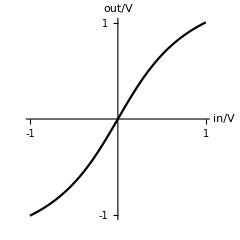

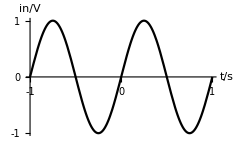

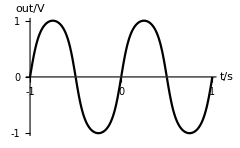

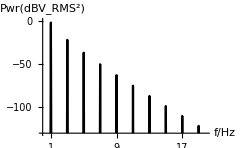

0.608704

THD = 0.102109

THD_R = 0.101581

```mathematica
Plot[ArcTan[x*π/2],{x,-1,1},AspectRatio->1,PlotTheme->"Monochrome",Ticks->{{-1,1},{-1,1}},AxesLabel->{"in/V","out/V"}]
Plot[Sin[2 π t] ,{t,-1,1},PlotTheme->"Monochrome",Ticks->{{-1,0,1},{-1,0,1}},AxesLabel->{"t/s","in/V"},AxesOrigin->{-1,0}]
Plot[ArcTan[Sin[2 π t] π/2],{t,-1,1},PlotTheme->"Monochrome",Ticks->{{-1,0,1},{-1,0,1}},AxesLabel->{"t/s","out/V"},AxesOrigin->{-1,0}]
sig=Table[ArcTan[Sin[2 π t] π/2],{t,0,9.99,0.01}];
pwr=(Abs[Fourier[sig]/√250]/√2)^2;
pwrdb=10*Log10[pwr];
freq=Table[f,{f,0,99.9,0.1}];
ps=Table[{freq[[i]],pwrdb[[i]]},{i,1,200}];
ListLinePlot[ps,PlotRange->{-130,0},AxesOrigin->{0,-130},PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"}]
ptotal=Total[Table[pwr[[i]],{i,11,Length[pwr]/2,10}]]
Print["THD = ",√((ptotal-pwr[[11]])/pwr[[11]])]
Print["THD_R = ",√((ptotal-pwr[[11]])/ptotal)]
```

```mathematica
0.102109/(√(1+0.102109))
```

0.0972639